```mathematica
ex={{"Per-Node\nLog Parsing",71},{"Per-Node\nPreprocessing",17.91},{"5 node\nClustering",.48},{"100 node\nClustering",2.1}}
BarChart[Last[#]&/@ex,ChartLabels->Placed[(First[#]&/@ex),Top],Frame->True,ChartElementFunction->"Rectangle",Axes->True,ChartStyle->24,FrameLabel->{"Compute Type","CPU usage per node (s)"},BaseStyle->{FontSize->40,FontFamily->"Calibri"}, ImageSize->1500]
```

{{Per-Node
Log Parsing,71},{Per-Node
Preprocessing,17.91},{5 node
Clustering,0.48},{100 node
Clustering,2.1}}

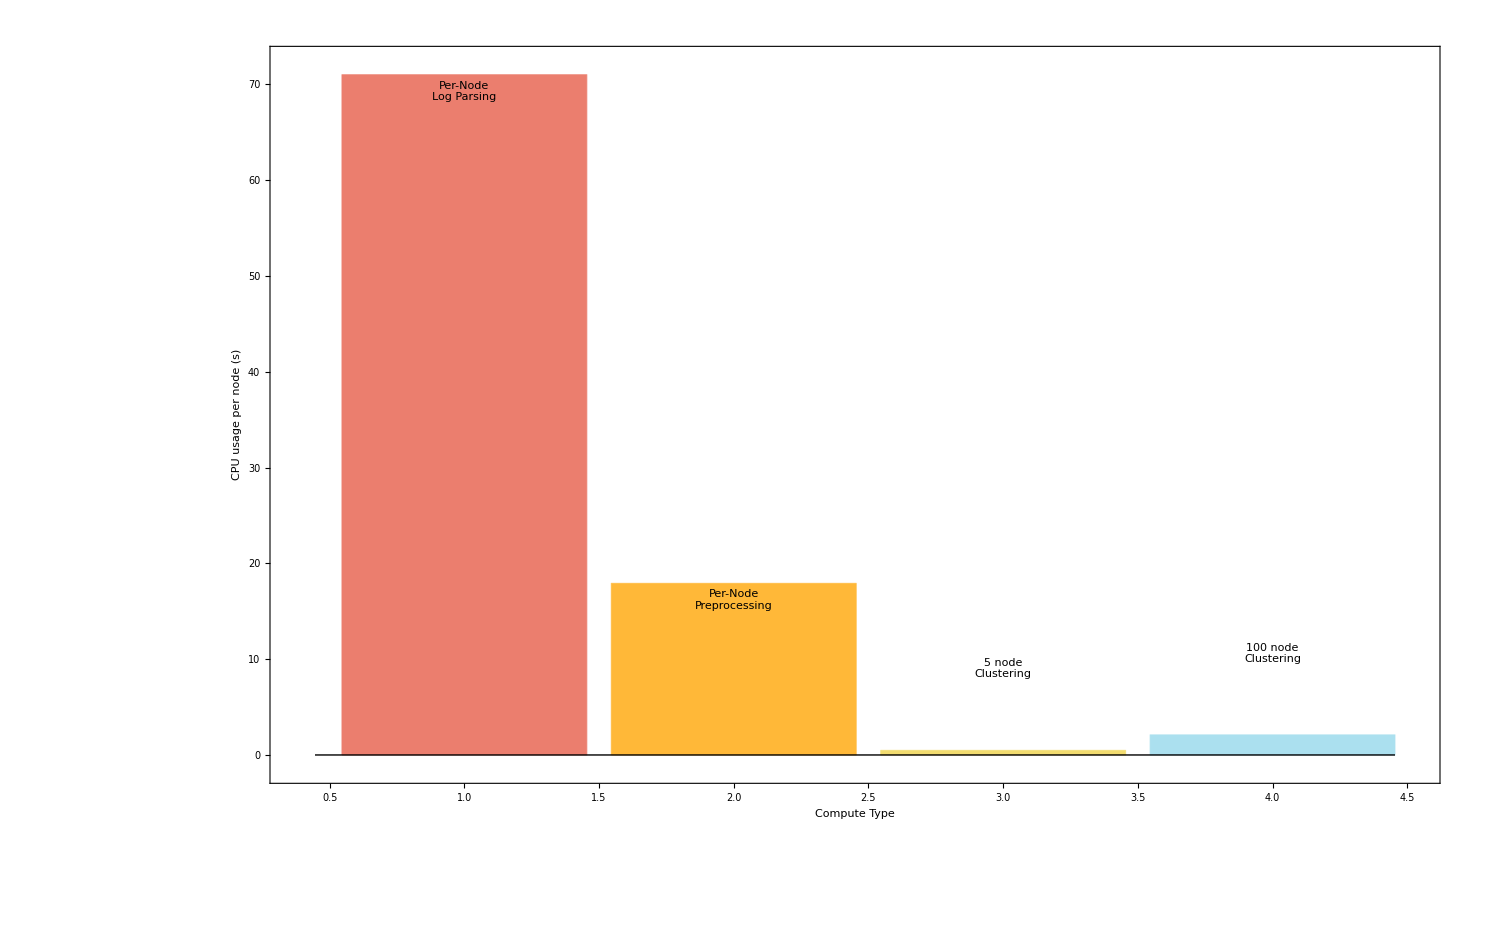

{{Failed node,2},{Node 5%
slower,2},{Node 1%
slower,3},{50% of log
is junk,2},{99% of log
is junk,4}}

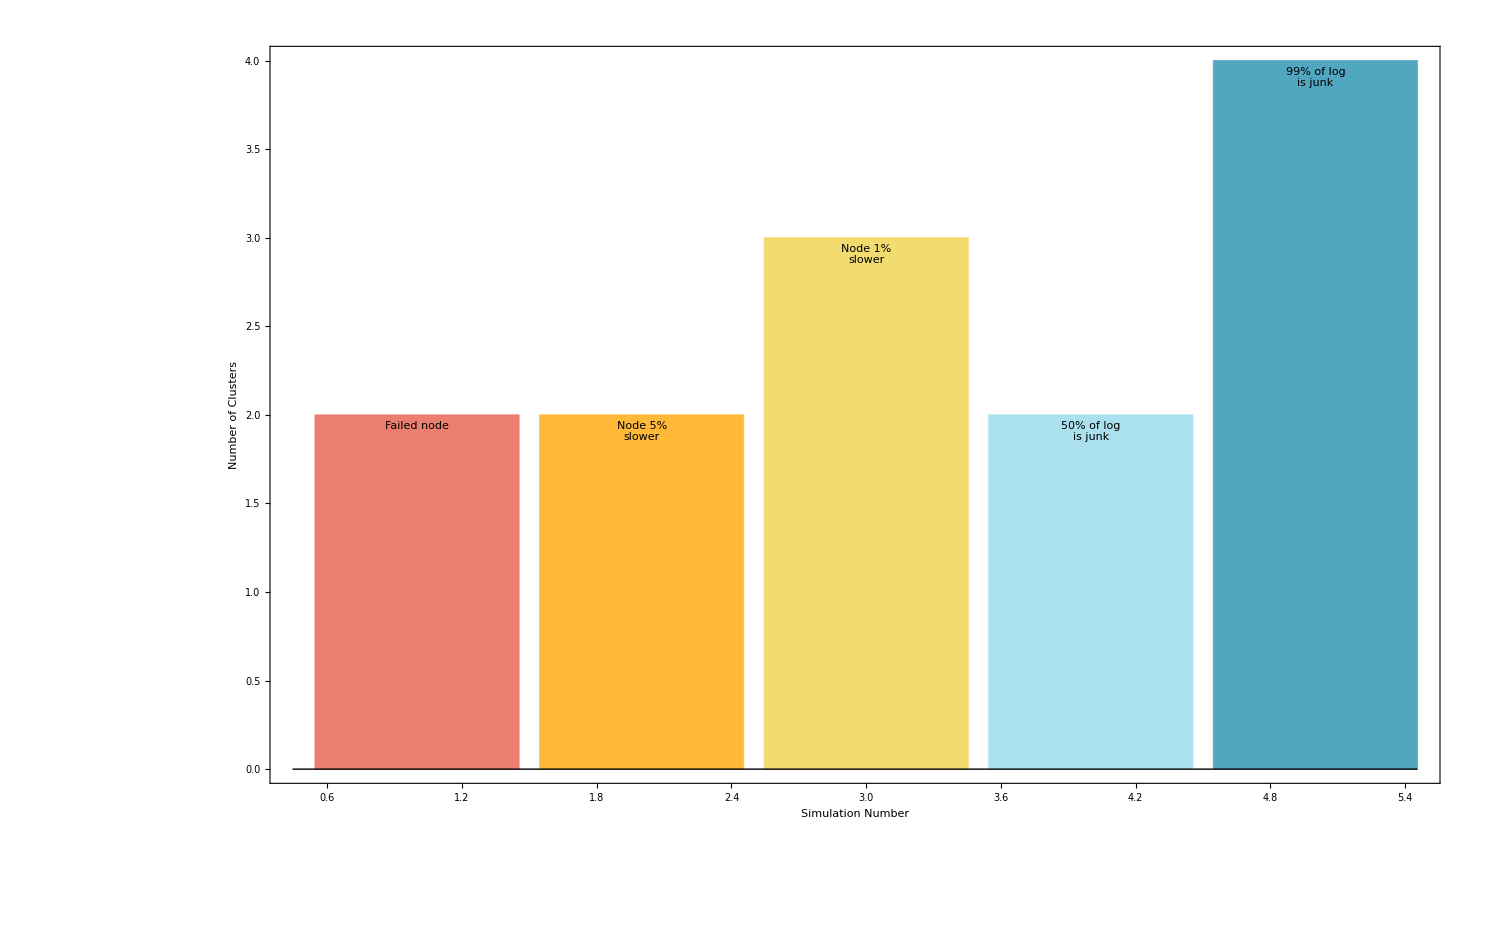

```mathematica
ex={{"Failed node",2},{"Node 5%\nslower",2},{"Node 1%\nslower", 3},{"50% of log\nis junk", 2}, {"99% of log\nis junk", 4}}
BarChart[Last[#]&/@ex,ChartLabels->Placed[(First[#]&/@ex),Top],Frame->True,ChartElementFunction->"Rectangle", Axes->True,ChartStyle-> 24,FrameLabel->{"Simulation Number" ,"Number of Clusters"},BaseStyle->{FontSize->40,FontFamily->"Calibri"}, ImageSize->1500]
```